# Two-frequency diagnostic result

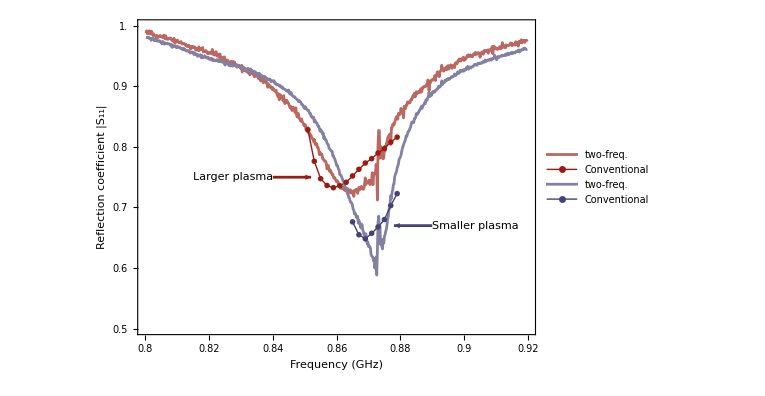

```mathematica
(* -- import data -- *)
dt=Import[NotebookDirectory[]<>"data.mx"];

(* -- plot -- *)
gf=ListLinePlot[

{dt[[1]],dt[[2,;;;;10]],dt[[3]],dt[[4,;;;;10]]},

Epilog->{
{Text[Framed[Style["Larger plasma",{FontColor->White,FontSize->14,FontWeight->Plain}],Background->RGBColor[0.6, 0.11, 0.07, 1],FrameStyle->Directive[Transparent,AbsoluteThickness[1]]],
{840,.75},{1,0}]},
{RGBColor[0.6, 0.11, 0.07, 1],AbsoluteThickness[2],Arrowheads[{0,.02}],Arrow[{{840,.75},{852,.75}}]},
{Text[Framed[Style["Smaller plasma",{FontColor->White,FontSize->14,FontWeight->Plain}],Background->RGBColor[0.27, 0.26, 0.46, 1],FrameStyle->Directive[Transparent,AbsoluteThickness[1]]],
{890,.67},{-1,0}]},
{RGBColor[0.27, 0.26, 0.46, 1],AbsoluteThickness[2],Arrowheads[{0,.02}],Arrow[{{890,.67},{878,.67}}]}
},

Joined->True,
PlotRange->{{800,920},{.5,1}},
PlotRangePadding->0,

PlotStyle->{
{RGBColor[0.7333333333333333, 0.4066666666666666, 0.37999999999999995, 1],AbsoluteThickness[2]},
{RGBColor[0.6, 0.11, 0.07, 1],AbsoluteThickness[1]},
{RGBColor[0.5133333333333333, 0.5066666666666666, 0.64, 1],AbsoluteThickness[2]},
{RGBColor[0.27, 0.26, 0.46, 1],AbsoluteThickness[1]}
},

PlotMarkers->{
None,
Graphics[{FaceForm[Transparent],EdgeForm[{RGBColor[0.6, 0.11, 0.07, 1],AbsoluteThickness[1]}],Disk[{0,0},Offset[3]]}],
None,
Graphics[{FaceForm[Transparent],EdgeForm[{RGBColor[0.27, 0.26, 0.46, 1],AbsoluteThickness[1]}],Disk[{0,0},Offset[3]]}]
},

PlotLegends->
Placed[
LineLegend[
{Directive[RGBColor[0.7333333333333333, 0.4066666666666666, 0.37999999999999995, 1],AbsoluteThickness[2]],Directive[RGBColor[0.6, 0.11, 0.07, 1],AbsoluteThickness[1]],
Directive[RGBColor[0.5133333333333333, 0.5066666666666666, 0.64, 1],AbsoluteThickness[2]],Directive[RGBColor[0.27, 0.26, 0.46, 1],AbsoluteThickness[1]]},
{"two-freq.","Conventional","two-freq.","Conventional"},
LegendMarkerSize->30,
LabelStyle->{FontColor->Black,FontSize->14,FontWeight->Plain},
LegendMargins->1,LegendLayout->{"Row",2}],
{Scaled@{.05,.05},{0,0}}
],

Axes->False,
Frame->True,
FrameLabel->{{"Reflection coefficient |S_11|",None},{"Frequency (GHz)",None}},
FrameTicks->{
{Table[{i,i,{.015,0}},{i,.5,1,.1}],
Table[{i,Null,{.015,0}},{i,.5,1,.1}]},
{Table[{i,If[Mod[i,20]==0,N@(i/1000),Null],{If[Mod[i,20]==0,.015,.008],0}},{i,800,920,5}],
Table[{i,Null,{If[Mod[i,20]==0,.015,.008],0}},{i,800,920,5}]}
},
FrameStyle->Directive[Black,AbsoluteThickness[1]],

LabelStyle->{FontColor->Black,FontFamily->"Arial",FontSize->9*2,FontWeight->Plain},

GridLines->Full,

PlotRangeClipping->False,
ImageSize->(100*2)*(72/25.4),
AspectRatio->.7

];

Print[gf];

Export[NotebookDirectory[]<>"comparison.pdf",gf];
```